```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
dz2[n_, z_, k_] := Sum[ dz[j,z]dz2[n/j,z,k-1],{j,2,n}]; dz2[n_, z_, 0] := UnitStep[n-1]
dd[n_, z_, x_] := Sum[ Binomial[x,k]dz2[n,z,k],{k,0,Log[2,n]}]
ddb[n_, z_, k_] := Sum[ dz[j,z]ddb[n/j,z,k-1],{j,1,n}]; ddb[n_, z_, 0] := UnitStep[n-1]
Clear[D2,D2a]
D2[n_, k_] := D2[n,k]=Sum[ D2[Floor[n/j],k-1],{j,2,n}]; D2[n_, 0]:= UnitStep[n-1]
d2[n_, k_] := D2[n,k]-D2[n-1,k]
Dz[n_, z_] := Sum[ bin[ z,k]D2[n,k],{k,0,Log[2,n]}]
Ez[n_, t_] := Sum[ Dz[n,k]/k!,{k,0,t}]
E2z[n_] := Sum[ D2[n,k]/k!,{k,0,Log[2,n]}]
D2a[n_, x_, k_] := D2a[n,x,k]=Sum[d2[j,x] D2a[Floor[n/j],x,k-1],{j,2,n}]; D2a[n_, x_, 0]:= UnitStep[n-1]
Clear[K,P,pp,Pz, P1zz]
K[n_] := K[n] = FullSimplify[ MangoldtLambda[n] / Log[n]]
P[n_, k_] := P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}]
P[n_, 0] := UnitStep[n-1]
pp[n_, k_] := P[n,k]-P[n-1,k]
Pz[n_, z_, k_] := Pz[n,z,k]=Sum[ pp[j,z]Pz[Floor[n/j],z,k-1],{j,2,n}]
Pz[n_, z_, 0] := UnitStep[n-1]
pz[n_, z_, k_] := Pz[n,z,k]-Pz[n-1,z,k]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
P1z[ n_, z_] := Sum[ bin[z,k]P[n,k],{k,0,Log[2,n]}]
p1z[n_, z_] := P1z[n,z]-P1z[n-1,z]
P1zz[n_, z_, k_] := P1zz[n,z,k]=Sum[ p1z[j,z]P1zz[Floor[n/j],z,k-1],{j,2,n}]
P1zz[n_, z_, 0] := UnitStep[n-1]
P1x[n_, z_, x_] := Sum[ Binomial[x,k]P1zz[n,z,k],{k,0,Log[2,n]}]
```

```mathematica
dz2[100,2,2]
```

2612

```mathematica
dd[100,3,3]
```

68494

```mathematica
dd[100,-1,-1]
```

100

```mathematica
ddb[100,3,3]
```

68494

```mathematica
D2a[5000,3,3]
```

6478

```mathematica
D2[5000,9]
```

6478

```mathematica
N@Log[(3^4)^5]
```

21.9722

```mathematica
N@(5Log[(3^4)])
```

21.9722

```mathematica
N@(20Log[(3)])
```

21.9722

```mathematica
Sum[ d2[j,2]D2[100/j,3],{j,2,100}]
```

51

```mathematica
D2[100,5]
```

51

```mathematica
D2a[100,2,3]
```

7

```mathematica
P[1000,6]
```

7547/4

```mathematica
{Pz[1000,6,1],Pz[1000,3,2],Pz[1000,2,3],Pz[1000,1,6]}
```

{7547/4,7547/4,7547/4,7547/4}

```mathematica
{D2a[1000,6,1],D2a[1000,3,2],D2a[1000,2,3],D2a[1000,1,6]}
```

{5048,5048,5048,5048}

```mathematica
pz[2^4 3 5 7,2,3]
```

180

```mathematica
pz[2^4 3 5 7,1,6]
```

180

```mathematica
pp[2^4 3 5 7,6]
```

180

```mathematica
Sum[ pp[j,3]pp[k,3]pp[l,3],{j,2,1000},{k,2,1000/j}, {l,2,1000/(j k)}]
```

10

```mathematica
P[1000,9]
```

10

```mathematica
mm[n_] := MoebiusMu[n]
1-Sum[ mm[j],{j,2,30}]+Sum[ mm[j]mm[k],{j,2,30},{k,2,30/j}]-Sum[ mm[j]mm[k]mm[l],{j,2,30},{k,2,30/j},{l,2,30/(j k)}]+Sum[ mm[j]mm[k]mm[l]mm[m],{j,2,30},{k,2,30/j},{l,2,30/(j k)},{m,2,30/(j k l)}]-Sum[ mm[j]mm[k]mm[l]mm[m]mm[o],{j,2,30},{k,2,30/j},{l,2,30/(j k)},{m,2,30/(j k l)},{o,2,30/(j k l m)}]
```

30

```mathematica
mm[n_] := 1 - Sum[ MoebiusMu[j] mm[n/j],{j,2,n}]
m2[n_,k_] := k - Sum[ MoebiusMu[j] m2[n/j,k+1],{j,2,n}]
d2[n_,k_] := k - Sum[ dz[j,2] d2[n/j,k+1],{j,2,n}]
mert[n_] := 1 - Sum[ mert[n/j],{j,2,n}]
```

```mathematica
mm[100]
```

100

```mathematica
mert[100]
```

1

```mathematica
dd[100,2,1/2]
```

100

```mathematica
1 + 2Sum[ dz[j,1/2],{j,2,100}]+ Sum[ dz[j,1/2]dz[k,1/2],{j,2,100}, {k,2,100/j}]
```

100

```mathematica
1 + 2Sum[ dz[j,3/2],{j,2,100}]+ Sum[ dz[j,3/2]dz[k,3/2],{j,2,100}, {k,2,100/j}]
```

1471

```mathematica
2*(1/2)
```

1

```mathematica
2*1/2
```

1

```mathematica
Series[ (x+1)^-2,{x,0,20}]
```

1-2 x+3 x^2-4 x^3+5 x^4-6 x^5+7 x^6-8 x^7+9 x^8-10 x^9+11 x^10-12 x^11+13 x^12-14 x^13+15 x^14-16 x^15+17 x^16-18 x^17+19 x^18-20 x^19+21 x^20+O[x]^21

```mathematica
m2[100,1]
```

482

```mathematica
SeriesCoefficient[(x+1)^(1/2),{x,0,0}]
```

1

```mathematica
dx[n_,z_, y_, k_] := SeriesCoefficient[(x+1)^(z),{x,0,k}] + Sum[ dz[j,y] dx[n/j,z, y, k+1],{j,2,n}]
```

```mathematica
dx[100,1/2,2,0]
```

100

```mathematica
Series[(x+1)^(-1),{x,0,20}]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16-x^17+x^18-x^19+x^20+O[x]^21

```mathematica
2*3/2
```

3

```mathematica
Sum[dz[j,3],{j,1,100}]
```

1471

```mathematica
Sum[ dz[k,2],{j,1,100}, {k,1,100/j}]
```

1471

```mathematica
Sum[ dz[j,1/2]dz[k,1/2],{j,1,100},{k,1,100/j}]
```

100

```mathematica
Sum[ dz[j,1/3]dz[k,1/3]dz[l,1/3],{j,1,100},{k,1,100/j},{l,1,100/(j k)}]
```

100

```mathematica
Sum[ dz[j,3]dz[k,1],{j,1,100},{k,1,100/j}]
```

3575

```mathematica
Sum[ (-1)^k (k+1) (x^-1 -1)^k,{k,0,Infinity}]
```

x^2

```mathematica
Expand@p1z[210,z]
```

-6 z+11 z^2-6 z^3+z^4

```mathematica
Table[D[Expand@dz[210,z],{z,k}],{k,0,5}]
```

{z^4,4 z^3,12 z^2,24 z,24,0}

```mathematica
dz[210,z]
```

z^4

```mathematica
P1zz[100,2,1]
```

26561/180

```mathematica
P1x[100,2,1/2]-1
```

428/15

```mathematica
Expand[(x^2-1)^2]
```

1-2 x^2+x^4

```mathematica
Sum[ ((Log[x]+1)^-1 -1)^k (-1)^k ,{k,0,Infinity}]
```

1+Log[x]

```mathematica
Sum[ Binomial[z,k](x-2)^k,{k,0,Infinity}]
```

(-1+x)^z

```mathematica
Clear[d3]
d3[n_, k_] := d3[n,k]=Sum[ d3[n/j,k-1],{j,3,n}]
d3[n_, 0] := UnitStep[n-1]
d2z[n_, z_] := Sum[ bin[z,k]d3[n/2^(z-k),k],{k,0,10}]
```

```mathematica
b2[100,1]+b2[100,0]
```

49

```mathematica
2b2[50,1]+1
```

97

```mathematica
b2[100/4,2]+2b2[100/4,1]+1
```

108

```mathematica
b2[100,2]
```

186

```mathematica
b2[100,2]
```

186

```mathematica
d2z[100,1]
```

99

```mathematica
Table[ bin[1.5,k]d3[100/2^(1.5-k),k],{k,0,12}]
```

{1,102.,114.375,-38.5,16.2188,-5.70703,1.41504,-0.188965,0.0271912,0.,0.,0.,0.}

```mathematica
Table[ bin[2.5,k]d3[100/2^(2.5-k),k],{k,0,12}]
```

{1,82.5,198.75,45.9375,-4.14063,0.539063,-0.0341797,0.00244141,0.,0.,0.,0.,0.}

```mathematica
Table[ bin[3.5,k]d3[100/2^(3.5-k),k],{k,0,12}]
```

{1,52.5,135.625,50.3125,2.46094,-0.0273438,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Table[ bin[3,k]d3[100/2^(3-k),k],{k,0,12}]
```

{1,69,183,71,0,0,0,0,0,0,0,0,0}

```mathematica
Table[ bin[3.3,k]d3[100/2^(3.3-k),k],{k,0,12}]
```

{1,59.4,159.39,67.4245,2.34341,-0.103603,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Table[ bin[4.3,k]d3[100/2^(4.3-k),k],{k,0,12}]
```

{1,34.4,70.95,21.758,1.76784,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Table[ bin[.5,k]d3[100/2^(.5-k),k],{k,0,12}]
```

{1,69.5,-99.75,132.375,-128.633,90.0156,-44.9736,15.2432,-3.10281,0.600052,-0.00927353,0.,0.}

```mathematica
Table[Sum[ bin[z,k]d3[16/2^(z-k),k],{k,0,12}],{z,.5,4.5,.1}]
```

{6.95313,9.01069,10.1273,11.6913,13.5019,15.,15.1797,16.136,16.8793,18.9424,18.5859,19.3264,17.422,19.168,17.5015,19.,15.0035,13.848,14.685,15.64,10.375,10.88,8.695,9.12,6.8,7.,4.1,4.2,4.3,4.4,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.}

```mathematica
Table[ bin[1.5,k]dd3[100/2^(1.5-k),k],{k,0,12}]
```

{dd3[35.3553,0],1.5 dd3[70.7107,1],0.375 dd3[141.421,2],-0.0625 dd3[282.843,3],0.0234375 dd3[565.685,4],-0.0117188 dd3[1131.37,5],0.00683594 dd3[2262.74,6],-0.00439453 dd3[4525.48,7],0.00302124 dd3[9050.97,8],-0.00218201 dd3[18101.9,9],0.00163651 dd3[36203.9,10],-0.00126457 dd3[72407.7,11],0.00100112 dd3[144815.,12]}

```mathematica
Table[ bin[4.5,k]dd3[100/2^(4.5-k),k],{k,0,12}]
```

{dd3[4.41942,0],4.5 dd3[8.83883,1],7.875 dd3[17.6777,2],6.5625 dd3[35.3553,3],2.46094 dd3[70.7107,4],0.246094 dd3[141.421,5],-0.0205078 dd3[282.843,6],0.00439453 dd3[565.685,7],-0.00137329 dd3[1131.37,8],0.000534058 dd3[2262.74,9],-0.000240326 dd3[4525.48,10],0.000120163 dd3[9050.97,11],-0.0000650883 dd3[18101.9,12]}

```mathematica
Table[ bin[.01,k]dd3[100/2^(.01-k),k],{k,0,20}]
```

{dd3[99.3092,0],0.01 dd3[198.618,1],-0.00495 dd3[397.237,2],0.0032835 dd3[794.474,3],-0.00245442 dd3[1588.95,4],0.00195862 dd3[3177.9,5],-0.00162892 dd3[6355.79,6],0.00139389 dd3[12711.6,7],-0.00121791 dd3[25423.2,8],0.00108124 dd3[50846.3,9],-0.000972031 dd3[101693.,10],0.000882781 dd3[203385.,11],-0.000808481 dd3[406771.,12],0.000745668 dd3[813541.,13],-0.000691873 dd3[1.62708×10^6,14],0.000645287 dd3[3.25417×10^6,15],-0.000604553 dd3[6.50833×10^6,16],0.000568636 dd3[1.30167×10^7,17],-0.000536729 dd3[2.60333×10^7,18],0.000508198 dd3[5.20666×10^7,19],-0.000482534 dd3[1.04133×10^8,20]}

```mathematica
d3[1000,6]
```

7

```mathematica
Floor[(1000/2^(4.5-10))/3^10]
```

0

```mathematica
If(n/2^(z-k))/3^k ≥ 1, then keep a-goin'
```

```mathematica
Log[(a+1)/a, n/a^z]/.{n->100,z->4.5,a->3}
```

-1.17694

```mathematica
d3[100,4]
```

1

```mathematica
Clear[da]
da[n_, k_,a_] := da[n,k,a]=Sum[ da[n/j,k-1,a],{j,a,n}]
da[n_, 0,a_] := UnitStep[n-1]
dap1z[n_, z_, a_] := Sum[ bin[z,k]da[n/a^(z-k),k,a+1],{k,0,10}]
dap1zt[n_, z_, a_] := Table[ bin[z,k]da[n/a^(z-k),k,a+1],{k,0,11}]
```

```mathematica
dap1zt[20,.5,3]
```

{1,15.5,-15.875,15.75,-11.1719,5.63281,-1.8457,0.241699,-0.013092,0.,0.,0.}

```mathematica
dap1zt[20,1.5,3]
```

{1,12.,4.5,-0.625,0.0234375,0.,0.,0.,0.,0.,0.,0.}

```mathematica
dap1zt[20,-.5,3]
```

$Aborted

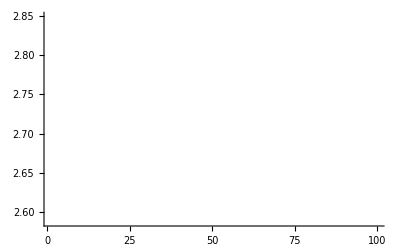

```mathematica
DiscretePlot[ Ez[n,30]/E2z[n],{n,1,100}]
```

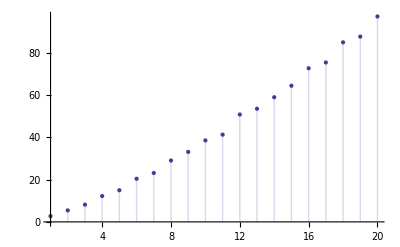

```mathematica
DiscretePlot[ Ez[n,30],{n,1,20}]
```

```mathematica
N@Ez[1,30]
```

2.71828

```mathematica
E2z[5]
```

11/2